Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. Convocatoria ordinaria: 10 enero 2025
F. Javier Muñoz delgado

Este examen supone entre 6 y 10 puntos de la nota final.
No se puede utilizar calculadora, ni reloj, sólo bolígrafo y papel.
Es fundamental que los razonamientos sean correctos y que los resultados sean correctos cuando se puedan comprobar y, si esto no es posible, que al menos los resultados no sean absurdos.

### 1.- Demostrar por inducción que 1*2 + 3*4 + 5*6 + ... + (2n-1)*(2n) , es decir ∑_(i=1)^n (2i-1)*(2i) , es igual a (1/3) n*(n+1)*(4n-1), para todo número natural n=1, 2, 3, ... . .

Solución:
Para realizar la demostración por inducción, comenzamos estudiando el primer caso, n=1. 
1) Caso n=1.
El primer término, que empieza con 1*2, debe terminar cuando n=1 con (2*1-1)*(2*1)=1*2, por tanto se reduce a un sumando. La igualdad que habría que comprobar es:
					 1*2=1/3*1*(1+1)*(4*1-1).
Es inmediato comprobar que ambas expresiones valen 2.
		1*2=2 	  			1/3*1*(1+1)*(4*1-1)=1/3*2*3=2
2) En la segunda parte del método de inducción, se supone que la propiedad es cierta para un valor n y se trata de comprobar que también lo sería para (n+1).

Es decir, si la igualdad es cierta para n, 
		1*2+3*4+5*6+...+(2n-1)*(2n)=1/3*n*(n+1)*(4n-1), 
se trataría de demostrar que también lo es para (n+1).

Escribimos la expresión para n+1.

1*2+3*4+5*6+...+(2n-1)*(2n)+(2(n+1)-1)*(2*(n+1))=1/3*(n+1)*((n+1)+1)*(4(n+1)-1) .

Para ver que es cierta esta nueva expresión, observamos que en la primera parte aparece la suma del caso n. Por tanto, usando que el caso n es cierto, escribimos

1*2+3*4+5*6+...+(2n-1)*(2n)+(2(n+1)-1)*(2*(n+1))=1/3*n*(n+1)*(4n-1)+(2(n+1)-1)*(2*(n+1))=1/3*n*(n+1)*(4n-1)+(2n+1)*(2n+2) . 

La segunda parte de la expresión del caso n+1 es:

	1/3*(n+1)*((n+1)+1)*(4(n+1)-1)=1/3*(n+1)*(n+2)*(4n+3).

Por tanto, tendríamos que comprobar que 

	1/3*n*(n+1)*(4n-1)+(2n+1)*(2n+2)=1/3*(n+1)*(n+2)*(4n+3).

O lo que es lo mismo, dividiendo por (n+1) y multiplicando por 3, hay que comprobar que:

	n*(4n-1)+3*(2n+1)*2=(n+2)*(4n+3).

Operando en ambos lados, obtenemos que la expresión de la izquierda vale:
	n*(4n-1)+3*(2n+1)*2=4 n^2-n+12n+6=4 n^2+11n+6

Y la segunda expresión vale:
	(n+2)*(4n+3)=4 n^2+3n+8n+6=4 n^2+11n+6

Se obtiene idéntico resultado en los dos miembros de la expresión y concluimos que de ser cierta la igualdad para n, también lo es para (n+1). 

Habiendo realizado los dos pasos de las demostraciones por el método de inducción, concluimos que la igualdad es cierta para todo número natural, n = 1, 2, 3, ...

## 2.- Resolver la ecuación | |x-3|-2 | = 1.

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión puede tomar dos valores, a ó -a. Sabiendo esto, obtenemos:
	 ||x-3|-2|=1 ⟹ |x-3|-2=1 ó  |x-3|-2=-1 
En el primer caso, 	 |x-3|-2=1 ⟹ |x-3|= 3 ⟹ x-3= 3 ó -3 ⟹ x = 3+3 ó x =-3+3 ⟹ x = 6 ó 0
En el segundo caso,  |x-3|-2=-1 ⟹ |x-3|= 1 ⟹ x-3= 1 ó -1 ⟹ x = 1+3 ó x =-1+3 ⟹ x = 4 ó 2

Hay 4 soluciones: 0, 2, 4 y 6.

Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-3]-2]==1,x,Reals]
```

x==0||x==2||x==4||x==6

## 3.- Calcular las raíces cúbicas del número complejo ((3 + ⅈ)/(2 - ⅈ)) .

Solución:
Comenzamos calculando el cociente que aparece. Para ello multiplicamos y dividimos por el conjugado del denominador.
		(3+ⅈ)/(2-ⅈ) = ((3+ⅈ)(2+ⅈ))/((2-ⅈ)(2+ⅈ)) = (6+5ⅈ+ ⅈ^2)/(4+1) = (5+5ⅈ)/5 = 1 + ⅈ  

Para calcular las raíces, es conveniente escribir el número en forma polar.

El argumento de 1 + ⅈ es π/4, pues está en la bisectriz del primer cuadrante (parte real y parte imaginaria positivas e iguales).
El módulo es √(1^2+1^2)=√2

Las tres raíces cúbicas del número complejo 1 + ⅈ tendrán el mismo módulo; la raíz cúbica de su módulo. Los argumentos serán: un tercio del argumento de 1 + ⅈ, un tercio del argumento de 1 + ⅈ  más un tercio de vuelta completa y un tercio del argumento de 1 + ⅈ  más dos tercios de vuelta.

	(1+ⅈ)^(1/3)= ((√2)_(π/4))^(1/3)= {(2^(1/6))_((π/4)/3),  (2^(1/6))_((π/4)/3+(2π)/3),  (2^(1/6))_((π/4)/3+2(2π)/3)} = {(2^(1/6))_(π/12),  (2^(1/6))_(π/12+(2π)/3),  (2^(1/6))_(π/12+(4π)/3)} = 
				{(2^(1/6))_(π/12),  (2^(1/6))_((9π)/12),  (2^(1/6))_((17π)/12)} .

## 4.- Calcular, si existe, el límite de la sucesión {√(n^2+3n+1)-√(n^2-2n+3)} .

Solución:
Nos encontramos con la diferencia de dos expresiones que se hacen cada vez mas grandes y tienden a infinito: tendríamos una indeterminación.

Para tratar de resolver el problema, multiplicamos y dividimos por el “conjugado”:
	√(n^2+3n+1)-√(n^2-2n+3)= ((√(n^2+3n+1)-√(n^2-2n+3))(√(n^2+3n+1)+√(n^2-2n+3)))/(√(n^2+3n+1)+√(n^2-2n+3))=  ((n^2+3n+1) - (n^2-2n+3)))/(√(n^2+3n+1)+√(n^2-2n+3))= (5n-2)/(√(n^2+3n+1)+√(n^2-2n+3))

El numerador es un polinomio de grado 1. El denominador no es un polinomio, pero es una suma dos raíces cuadradas de polinomios de grado dos, es decir, en cierta medida sería parecido a polinomios de grado 1, por ello dividimos por n, numerador y denominador:
	(5n-2)/(√(n^2+3n+1)+√(n^2-2n+3))= ((5n)/n-2/n)/((√(n^2+3n+1))/n+ (√(n^2-2n+3))/n) = (5 - 2/n)/(√((n^2+3n+1)/n^2) + √((n^2-2n+3)/n^2)) = (5 - 2/n)/(√(1+3/n+1/n^2) + √(1-2/n+3/n^2))  ⟶  5/(√(1+0+0)+ √(1+0+0))=5/2.

La n puede entrar en la raíz cuadrada como n^2. Simplificando y haciendo que n tienda a infinito, nos encontramos que el límite vale 5/2.

Con el Mathematica,

```mathematica
Limit[√(n^2+3*n+1)-√(n^2-2n),n->Infinity]
```

5/2

## 5.- Calcular la suma de la serie ∑_(n=1)^∞ (6n+12)/(n^3+4 n^2+3n).

Solución:
Dado que la diferencia de grados entre numerador y denominador es de 2 a favor del denominador, la serie converge. Para sumar, descomponemos la fracción en suma de fracciones simples. Para ello hallamos las raíces del denominador:
		 n^3+4 n^2+3n=n(n^2+4n+3)=0 ⟹ n=0 ó n^2+4n+3=0 ⟹ (Resolviendo la ecuación de segundo grado)  n=0 ó n = -1 ó n = -3
		  
		a_n= (6n+12)/(n^3+4 n^2+3n) = (6n+12)/(n(n^2+4n+3)) = (6n+12)/(n(n+1)(n+3)) = A/n + B/(n+1) + C/(n+3)=(A(n+1)(n+3)+Bn(n+3)+Cn(n+1))/(n(n+1)(n+3))
		
		6n+12 = A(n+1)(n+3) + Bn(n+3) + Cn(n+1)
Para encontrar A, B y C, sustituimos en la expresión anterior n por 0, -1 y -3:

	n=0		6*0+12= A(0+1)(0+3)+B*0*(0+3)+C*0*(0+1) ⟹ 12= 3A ⟹ A= 4
	n=-1		6*(-1)+12= A(-1+1)(-1+3)+B*(-1)*(-1+3)+C*(-1)*(-1+1) ⟹ 6= -2B ⟹ B= -3
	n=-3		6*(-3)+12= A(-3+1)(-3+3)+B*(-3)*(-3+3)+C*(-3)*(-3+1) ⟹ -6= 6C ⟹ C= -1

	a_n= (6n+12)/(n^3+4 n^2+3n) = (6n+12)/(n(n^2+4n+3)) = (6n+12)/(n(n+1)(n+3)) = 4/n - 3/(n+1) - 1/(n+3)

S_n=4/1-3/(1+1)-1/(1+3)+4/2-3/(2+1)-1/(2+3)+4/3-3/(3+1)-1/(3+3)+4/4-3/(4+1)-1/(4+3)+4/5-3/(5+1)-1/(5+3)+ ....+4/(n-3)-3/(n-2)-1/n+4/(n-2)-3/(n-1)-1/(n+1)+4/(n-1)-3/n-1/(n+2)+4/n-3/(n+1)-1/(n+3)=
(hacemos las sumas o restas indicadas)
=4/1-3/2-1/4+4/2-3/3-1/5+4/3-3/4-1/6+4/4-3/5-1/7+4/5-3/6-1/7 + .... +4/(n-3)-3/(n-2)-1/n+4/(n-2)-3/(n-1)-1/(n+1)+4/(n-1)-3/n-1/(n+2)+4/n-3/(n+1)-1/(n+3)=
(agrupamos las fracciones de igual denominador)
=(4/1)+(4/2-3/2)+(4/3-3/3)+(4/4-3/4-1/4)+(4/5-3/5-1/5)+ .... + (4/(n-1)-3/(n-1)-1/(n-1)) + (4/n-3/n-1/n) + (-3/(n+1)-1/(n+1)) +  (-1/(n+2))+ (-1/(n+3))=
(salvo las tres primeras agrupaciones y las tres últimas, el resto se anula)
=(4/1)+(4/2-3/2)+(4/3-3/3) + 0 + 0 + .... + 0 + 0 + (-3/(n+1)-1/(n+1)) +  (-1/(n+2))+ (-1/(n+3))=
=(4/1) + (1/2) + (1/3) - (4/(n+1)) - (1/(n+2)) -(1/(n+3))=
=(24/6) + (3/6) + (2/6) - (4/(n+1)) - (1/(n+2)) -(1/(n+3)) ⟶ 29/6

Con el Mathematica,

```mathematica
Sum[(6 (2+n))/(n (1+n) (3+n)),{n,1,Infinity}]
```

29/6

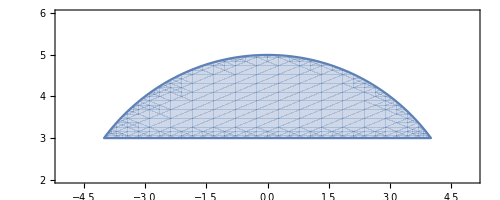
## 6.- Calcular la integral de la función f(x,y)= y, en la región de la figura, comprendida entre la recta y=3 y la circunferencia centrada en el (0,0) y de radio 5. -Graphics- (es decir, x^2+ y^2 ≤ 25, y ≥ 3).

Solución:
La región está limitada por la recta y el arco de circunferencia.

Los puntos de corte de las dos líneas se calculan resolviendo el sistema:
			y=3
		x^2+ y^2 = 25.
Sustituyendo el valor de y en la segunda ecuación:
		3^2+ y^2 = 25 ⟹ 3^2+ y^2 = 25

Vemos que x varía en el intervalo [-4,4]. Para cada valor de x, la y varía entre y=3 e y= √(25-x^2).
∫_-4^4 (∫_3^(√(25-x^2)) yⅆy)ⅆx=∫_-4^4 (y^2/2)|_(y=3)^(y=√(25-x^2))ⅆx =  ∫_-4^4 (((25-x^2) - 9)/2)ⅆx =  ∫_-4^4 (8-x^2/2)ⅆx = (8 x - x^3/6)|_(x=-4)^(x=4) = (8*4-4^3/6)-(8*(-4)-(-4)^3/6) = (32-64/6) - (-32--64/6) = (64-128/6) = (128/3) .
La integral vale 1/6.

```mathematica
∫_-4^4 (∫_3^(√(25-x^2)) yⅆy)ⅆx
```

128/3

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=y*(1-x^2-12 y^2) .

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		f(x,y)=y*(1-x^2-12 y^2) = y-x^2 y-12 y^3

		∂_x f(x,y) = -2xy = 0 ⟹ xy=0
		∂_y f(x,y) = 1-x^2-36 y^2 = 0

De la primera ecuación sabemos que x=0 ó y=0.
Si x=0, la segunda ecuación queda como 1-36 y^2 = 0. De donde y^2 = 1/36, es decir, y = 1/6 ó y = -1/6.
Si y=0, la segunda ecuación queda como 1-x^2 = 0. De donde x^2 = 1, es decir, x = 1 ó x = -1.

Las soluciones son (0,1/6), (0,-1/6), (1,0) y (-1,0). Esos son los puntos donde se anulan las dos derivadas parciales.

Para ver si son máximos, mínimos o puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(-2y | -2x
-2x | -72y)|
Hessiano (1,0) = |(0 | -2
-2 | 0)|= -4 < 0 (Punto de silla)
Hessiano (-1,0) = |(0 | 2
2 | 0)|= -4 < 0 (Punto de silla)
Hessiano (0,1/6) = |(-2/6 | 0
0 | -12)|= 4 > 0 (Habrá un máximo o mínimo local. Para saber si es máximo o mínimo, estudiamos la derivada segunda en la x o la y, en el punto en cuestión. Así, al ver que ∂_(x,x) f(0,1/6)=-2/6<0, concluimos que hay un máximo local.)
Hessiano (0,-1/6) = |(2/6 | 0
0 | 12)|= 4 > 0 (Habrá un máximo o mínimo local. Para saber si es máximo o mínimo, estudiamos la derivada segunda en la x o la y, en el punto en cuestión. Así, al ver que ∂_(x,x) f(0,-1/6)=2/6>0, concluimos que hay un mínimo local.)

Con el Mathematica:

```mathematica
f[x_,y_]:=y(1-x^2-12 y^2)
```

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→-1/6},{x→0,y→1/6},{x→-1,y→0},{x→1,y→0}}

Las derivadas parciales se anulan en 4 puntos. Para estudiar lo que ocurre en estos puntos, calculamos el hessiano de la función y evaluamos en los puntos encontrados.

```mathematica
hess[x_,y_]:=Det[({{D[f[u,v],{u,2}], D[f[u,v],{u,1},{v,1}]}, {D[f[u,v],{u,1},{v,1}], D[f[u,v],{v,2}]}})]/.{u->x,v->y}
```

```mathematica
hess[0,-1/6]
```

4

```mathematica
D[f[x,y],{x,2}]/.{x->0,y->-1/6}
```

1/3

En el punto (0,-1/6) el hessiano es mayor que cero, luego hay máximo o mínimo relativo. A la vista de que la derivada segunda en la primera variable es positiva, habrá un mínimo relativo.

```mathematica
hess[0,1/6]
```

4

```mathematica
D[f[x,y],{x,2}]/.{x->0,y->1/6}
```

-1/3

En el punto (0, 1/6) el hessiano es mayor que cero, luego hay máximo o mínimo relativo. A la vista de que la derivada segunda en la primera variable es negativa, habrá un máximo relativo.

```mathematica
hess[-1,0]
```

-4

En el punto (-1, 0) el hessiano es menor que cero, luego hay un punto de silla.

```mathematica
hess[1,0]
```

-4

En el punto (1, 0) el hessiano es menor que cero, luego hay un punto de silla.

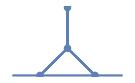
## 8.- Considerar los puntos (-1,0), (1,0) y (0,5). Encontrar el punto de la forma (0,α) con α entre 0 y 5 tal que -Graphics- la suma de las distancias de éste a los otros tres puntos sea mínima.

Solución:
La suma de las distancias, en función de α, es f(α) = (5-α) + 2 √(α^2+1^2) , con α en [0,5].
Se trata de una función continua en un intervalo cerrado y acotado. Por el teorema de Weierstrass, tiene máximo y mínimo absolutos. Los máximos y mínimos absolutos pueden estar en los extremos, en los puntos con derivada cero o en los puntos sin derivada.
La función es derivable. La derivada es f ’(α) = -1 + 2α/√(α^2+1).  Igualando la derivada a cero,  
		-1 + 2α/√(α^2+1) = 0 ⟹  2α =√(α^2+1) ⟹ 4 α^2 = α^2+1 ⟹ 3 α^2 = 1 ⟹ α^2 = 1/3 ⟹ α = 1/√3 (α = - 1/√3 no es solución, ni está en el dominio).

Ahora evaluamos en los extremos y en el punto de derivada cero. 
	f(0) = (5-0) + 2 √(0^2+1^2) = 5 + 2 √1 = 7, 
	f(5) = (5-5) + 2 √(5^2+1^2) = 2 √(5^2+1^2) = 2 √26  (Es mayor que 10),
	f(1/√3) = (5-1/√3)+2 √(1/3+1)= (5 √3-1)/√3+2 √(4/3)=(5 √3-1)/√3+4/√3 =(5 √3+3)/√3= 5 +√3 (es menor que 7).
	El mínimo es 5 +√3 y se alcanza cuando α = 1/√3. 

Con el Mathematica,

```mathematica
f[α_]:=(5-α)+2 √(α^2+1)
```

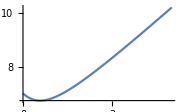

```mathematica
Plot[f[α],{α,0,5}]
```

```mathematica
Solve[f'[α]==0,α]
```

{{α→1/(√3)}}

```mathematica
{f[0],f[5],f[1/(√3)]}//N
```

{7.,10.198,6.73205}

Evaluando la función en los extremos del intervalo y en el punto de derivada cero, encontramos que el mínimo se encuentra en 1/(√3).

## 9.- Resolver la ecuación diferencial y’’ - y’ = 2x+1.

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y’ = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - x = 0; x(x-1) = 0; x=0 ó x=1.
	Si las soluciones de la ecuación polinómica son 0 y 1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^(0*x) +  C_2 ⅇ^(1*x) =  C_1 +  C_2 ⅇ^x, con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y’ = 2x + 1.
	Nos fijamos en que el término independiente es un polinomio de grado 1. Como las constantes son solución de la ecuación homogénea, elevamos el grado de los polinomios y probamos con una función del tipo  y_p(x) = a x + b x^2.
	y_p(x) = a x + b x^2
	y_p'(x) = a + 2 b x
	y_p''(x) = 2 b
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p' = 2b  - (a + 2 b x ) = 2b - a -2 b x = 2x+1
De donde 2b-a=1, -2b=2 . Por tanto, b=-1, a=2b-1=-2-1=-3
	La solución particular es  y_p(x) = -3x-x^2.
La solución general es y(x) = -3x-x^2+C_1 + C_2 ⅇ^x , con C_1 , C_2 números reales cualesquiera.

Con el Mathematica

```mathematica
DSolve[y''[x]-y'[x]==2x+1,y[x],x]
```

{{y[x]→-3 x-x^2+ⅇ^x C[1]+C[2]}}

## 10.- Calcular el polinomio de ℙ_3 que interpola f(1) = 1, f ‘(1) = 2, f ‘’(1)= -2, f (2) = 3.

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-1) + d (x-1) (x-1) (x-1).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,1] (x-1) + f[1,1,1] (x-1) (x-1) + f[1,1,1,2] (x-1) (x-1)(x-1)

f(1) = f[1] = 1, 	f[1,1] = f’(1) = 2 ,  	f[1,1,1] = f’’(1)/2!= -2/2=-1, 	f[1,1,1,2]=(f[1,1,2]-f[1,1,1])/(2-1)=(0-(-1))/(2-1)=1
f(1) = f[1] = 1, 	f[1,1] = f’(1) = 2,	f[1,1,2] = (f[1,2]-f[1,1])/(2-1) = (2-2)/(2-1)=0
f(1) = f[1] = 1, 	f[1,2] = (f[2]-f[1])/(2-1)= (3-1)/(2-1) = 2
f(2) = f[2] = 3

El polinomio que interpola es p(x) =  1 + 2 (x-1) - 1 (x-1) (x-1) +  (x-1) (x-1) (x-1) = -3+7x-4x^2+x^3
Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1,2,-2},{2,3}},x]
```

1+(2+(-2+x) (-1+x)) (-1+x)

```mathematica
Collect[%,x]
```

-3+7 x-4 x^2+x^3

## 11.- Estudiar la función f(x) = x^3-3x-5 para decidir si hay raíces en el intervalo [0,3]. Razonar desde cuál de los extremos del intervalo el método de Newton generaría una sucesión de puntos monótona convergente a una solución de f(x)=0. Realizar dos iteraciones a partir de dicho punto.

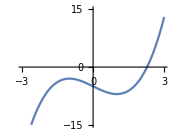
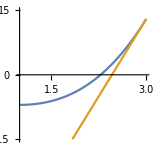
Solución:
La función es un polinomio de grado 3, es por tanto una función continua y derivable en toda la recta real.
	f(x) = x^3-3x-5; f ’(x) = 3 x^2-3; f ‘’(x) = 6x
	
	f(0) = -5<0,
	f(3) = 3^3-3*3-5= 27-9-5=13>0
	
	Al evaluar en los puntos 0 y 3, vemos que hay cambio de signo de la función f. Utilizando el teorema de Bolzano, como f es una función continua en el intervalo [0,3] y tiene signos opuestos en los extremos, podemos asegurar que hay al menos una raíz en [0,3].
	
	f ‘(x) = 3 x^2-3=0 ⟹ 3 x^2=3 ⟹ x^2=1 ⟹ x= -1 ó 1.
	
	La derivada de f(x) se anula en los puntos -1 y 1. Para conocer el crecimiento de f(x), evaluamos f ’(x) antes del -1 (por ejemplo, en -2), entre el -1 y el 1 (por ejemplo, el 0) y después del 1 (por ejemplo, el 2). 
			f ‘(-2) = 3*2^2-3 = 9
			f ‘(0) = 3*0^2-3=-3
			f ‘(2) = 3*2^2-3= 9
	Además, los valores de f en -1 y en 1 son:		
			f(-1) = (-1)^3-3(-1)-5=-3, f(1) = 1^3-3*1-5=-7
	Por tanto, f es creciente en (-∞,-1). En -1, donde f vale -3, hay un máximo local o relativo. En (-1,1), f es decreciente. En 1, donde f vale -7, hay un mínimo local o relativo. En (1,∞), f es creciente.
									-Graphics-
	La función f tiene una sola raíz, que sabemos debe estar entre el punto 1 (donde f vale -7) y el punto 3, donde f vale 13.
	Respecto a la derivada segunda, f ‘’(x) = 6x, tenemos que f ’’ es negativa en (-∞,0) y es positiva en (0,∞). Por tanto, f es cóncava (∩) en  (-∞,0) y es convexa (∪) en (0,∞). Hay un punto de inflexión de f en el punto 0.
	En el método de Newton, se calcula la tangente a la gráfica de la función en un punto inicial x0 y se calcula el punto donde la tangente corta al eje horizontal. Como f(x) es estrictamente creciente, y convexa en (1,3), donde f tiene una raíz. El teorema de convergencia del método de Newton nos asegura que partiendo del punto donde la derivada segunda y la función tienen el mismo signo, se genera una sucesión monótona convergente a una raíz de f(x).
											-Graphics-
	f(x) = x^3-3x-5
	f ‘(x) = 3 x^2-3
	x0=3
	x1=x0-f(x0)/f’(x0)= 3 - f(3) / f’(3) = 3 - (3^3-3*3-5) /(3*3^2-3) = 3 - (27-9-5)/(27-3) = 3 - 13/24 = (72-13)/24 = 59/24 
	x2=x1-f(x1)/f’(x1)= 59/24 - f(59/24) / f’(59/24) = (59/24) - ((59/24)^3-3*59/24-5) /(3*(59/24)^2-3)

## 12.- Dada la integral ∫_0^2 (1+2x)/(1+x+x^2)ⅆx , calcular su valor exacto. Aproximar también su valor utilizando la fórmula de Simpson simple.

Solución:
Para calcular la integral definida, calculamos una primitiva de la función.

			∫_0^2 (1+2x)/(1+x+x^2)ⅆx
Observamos que se trata de un cociente, donde el numerador es la derivada del denominador, por tanto

			∫_0^2 (1+2x)/(1+x+x^2)ⅆx = Log |1+x+x^2||_(x=0)^(x=2) = Log |1+2+2^2|- Log |1+0+0^2|= Log 7 - Log  1 = Log 7

El método de Simpson consiste en aproximar la integral definida de una función en un intervalo [a,b] utilizando los valores de la función en los extremos y en el punto medio.
	∫_a^b f(x)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a)
En este caso,
	∫_0^2 (1+2x)/(1+x+x^2)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a) =  (f(0)+4 f((0+2)/2)+f(2))/6 (2-0)= ((1/1) + 4 ((1+2)/(1+1+1))+(5/7))/3 = (1+4 + 5/7)/3=((7+28+5)/7)/3=40/21
	
Con el Mathematica,

```mathematica
f[x_]:= (1+2x)/(1+x+x^2)
```

```mathematica
2(f[0]+4f[1]+f[2])/6
```

40/21

```mathematica
∫_0^2 f[x]ⅆx
```

Log[7]

## 13.- Calcular la función spline de grado 2 y clase 1, con nodos 0, 1 y 2, que interpola los datos f(0)=0, f(1)=0, f(2)=0, f ‘(0) = π.

Solución:
Tenemos que buscar un polinomio en el intervalo [0,1] y otro en el [1,2]. Los dos polinomios deben ser de grado menor o igual a dos y deben “unir” con clase 1 en el punto 1 (es decir, deben tener el mismo valor en el punto 1 y la misma derivada).
s(x)=Piecewise[{{p1(x) =a+b(x-0)+(c(x-0))^2, 0≤x≤1}, {p2(x)=d+e(x-1)+(f(x-1))^2, 1≤x≤2}}]
Para calcular el polinomio p1(x) usamos los datos: f(0)=0, f ‘(0)=π, f (1)= 0
p1(0)=a+0+0 = 0
p1’(0)=0+b+0 = π
p1(1)=a+b*1+c*1^2=0+π  + c=0 ⟹ c=-π

Una vez calculado el polinomio p1(x) = π * x - π  x^2, calculamos su derivada en el punto 1, p1’(x) = π - 2*π *x, p1’(1)=π - 2*π *1 = π - 2*π   = - π .
El polinomio p2(x) debe cumplir
p2(1) = d + 0 + 0 = 0
p2’(1) = 0 + e + 0 = -π 
p2(2) = d + e* (2-1) + f*(2-1)^2 = 0 - π  + f  = -π  + f = 0  ⟹ f = π 

Por tanto, el polinomio p2(x)=-π(x-1)+π (x-1)^2 y tenemos calculada la función spline.

s(x)=Piecewise[{{p1(x) =π * x-π  x^2, 0≤x≤1}, {p2(x)=-π(x-1)+π (x-1)^2, 1≤x≤2}}]

Con el Mathematica

```mathematica
p1[x_]:=a + b (x-0)+ c (x-0)^2
```

```mathematica
p2[x_]:= d + e (x-1) + f (x-1)^2
```

```mathematica
Solve[{p1[0]==0,p1'[0]==π,p1[1]==0,p2[1]==0, p1'[1]==p2'[1],p2[2]==0},{a,b,c,d,e,f}]
```

{{a→0,b→π,c→-π,d→0,e→-π,f→π}}

```mathematica
{p1[x],p2[x]}/.%
```

{{π x-π x^2,-π (-1+x)+π (-1+x)^2}}

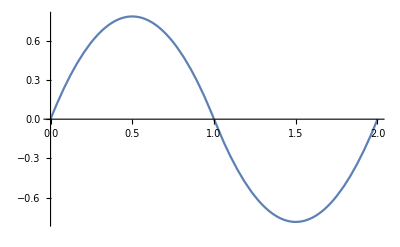

```mathematica
Plot[Which[0≤x≤1,π x-π x^2,1≤x≤2,-π (-1+x)+π (-1+x)^2],{x,0,2}]
```

## 14.- Utilizando el método de Taylor de segundo orden, aproximar el valor de y(4), siendo y(x) la solución de la ecuación diferencial y’ = y + x - 1 con la condición inicial y(0)=1. Dar dos saltos con paso h=2.

Solución:
Se trata de aproximar la solución de una ecuación diferencial con una condición inicial en un punto. 
La ecuación diferencial es y’ =  y + x - 1. 
La condición inicial es y(0)=1. 
Hay que aproximar el valor de y(4).
El método para hacerlo es el de Taylor de segundo orden. Este método, utiliza no solo la primera derivada (como hace el método de Euler), también usa la derivada segunda para tratar de avanzar con más precisión en cada salto.
El salto se hace con paso h=2. Por tanto, necesitaremos dar dos saltos para llegar  al punto 4.

La primera derivada de y, y’, es igual a y+x-1=f(x,y).
La segunda derivada de y será:
y’’ = (y’)’ = (y+x-1)’ = y’ + 1 + 0 = (y+x-1) + 1 = y + x  =g(x,y)

Utilizando la primera y segunda derivada, la aproximación por Taylor en cada punto vendrá dada por 
y_(i+1)=y_i+h f(x_i, y_i)+h^2/2 g(x_i, y_i)

En nuestro caso;
f(x,y) = x+y-1;
g(x,y)=x+y;
h=2
x_0=0; 
x_1=x_0+ h=0+2=2; 
x_2=x_1+h = 2+2=4; 
y_0=1;
y_1=y_0+h f(x_0, y_0)+h^2/2 g(x_0, y_0) ⟹ y_1=1+2* f(0_, 1_)+2^2/2 g(0, 1_) = 1+ 2*f(0_, 1_)+2g(0, 1_) = 1+2*(0+1-1)+2*(0+1) = 1+2*0+2*1 = 3
y_2=y_1+h f(x_1, y_1)+h^2/2 g(x_1, y_1) ⟹ y_2=3+2* f(2_, 3_)+2^2/2 g(2, 3_) = 3+ 2*f(2_, 3_)+2*g(2, 3_) = 3+2*(2+3-1)+2*(2+3) =  3+2*4+2*5 = 3+8+10 = 21.
La aproximación de y(4) por el método de Taylor de segundo orden sería 21.

Con el Mathematica,

```mathematica
f[x_,y_]:=x+y-1
```

```mathematica
g[x_,y_]:=(D[f[u,v],u]+D[f[u,v],v]*f[u,v])/.{u->x,v->y}
```

```mathematica
g[x,y]
```

x+y

```mathematica
h=2;x0=0;x1=x0+h;x2=x1+h;y0=1;
```

```mathematica
y1=y0+h*f[x0,y0]+h^2/2 g[x0,y0]
```

3

```mathematica
y2=y1+h*f[x1,y1]+h^2/2 g[x1,y1]
```

21